# For Gianluca

# Analytic calculations checks

## A checks - output checking

Lets define first the

```mathematica
(* Mathematica has internat function to generate a discrete Fourier transform matrix *)
UFT1 = FourierMatrix[2];
UFT2 = FourierMatrix[4];
```

Lets define the Q operator

```mathematica
(* Generated by the 4 Pauli strings on 1 qubit but taken to 4 times replicated space *)
PauliString1[i_]:=PauliMatrix[i];
Q1=(1/4)*Sum[KroneckerProduct[PauliString1[i],PauliString1[i],PauliString1[i],PauliString1[i]],{i,0,3}];

(* Generated by the 16 Pauli strings on 2 qubits but taken to 4 times replicated space *)
PauliString2[i_,j_]:=KroneckerProduct[PauliMatrix[i],PauliMatrix[j]];
Q2=(1/16)*Sum[KroneckerProduct[PauliString2[i,j],PauliString2[i,j],PauliString2[i,j],PauliString2[i,j]],{i,0,3},{j,0,3}];

(* Generated by the 16 Pauli strings on 2 qubits but taken to 4 times replicated space *)
PauliString3[i_,j_,k_]:=KroneckerProduct[SparseArray[PauliMatrix[i]],SparseArray[PauliMatrix[j]],SparseArray[PauliMatrix[k]]];
Q3=(1/64)*Sum[KroneckerProduct[PauliString3[i,j,k],PauliString3[i,j,k],PauliString3[i,j,k],PauliString3[i,j,k]],{i,0,3},{j,0,3},{k,0,3}];

PauliString4[i_,j_,k_,l_]:=KroneckerProduct[SparseArray[PauliMatrix[i]],SparseArray[PauliMatrix[j]],SparseArray[PauliMatrix[k]],SparseArray[PauliMatrix[l]]];
```

Lets define the Permutation operator \Pi_sim

```mathematica
(* function to generate the pertunations *)
indexToQubitIndices[n_,numQubits_]:=PadLeft[IntegerDigits[n-1,2],numQubits];
permutationMatrix[permutation_]:=With[{numQubits=Length@permutation},SparseArray[{{i_,j_}:>1/;Equal[Permute[indexToQubitIndices[i,numQubits],permutation],indexToQubitIndices[j,numQubits]]},2^numQubits {1,1}]];

(* list the possible permutations of 1 qubit on 4 times replicated space *)
permsingle=Permutations@{1,2,3,4};

(* total operator reads *)
P1=(1/24)*Sum[permutationMatrix[Flatten[permsingle[[i]]]],{i,1,24}];

(* list the possible permutations of 2 qubits on 4 times replicated space *)
permdouble=Permutations@{{1,2},{3,4},{5,6},{7,8}};

(* total operator reads *)
P2=(1/24)*Sum[permutationMatrix[Flatten[permdouble[[i]]]],{i,1,24}];
(*
permtriple=Permutations@{{1,2,3},{4,5,6},{7,8,9},{10,11,12}};

P3=(1/24)*Sum[permutationMatrix[Flatten[permtriple[[i]]]],{i,1,24}];
*)
```

### Evaluation for 1 qubit

```mathematica
A1N1=Tr[ KroneckerProduct[ConjugateTranspose[UFT1],ConjugateTranspose[UFT1],ConjugateTranspose[UFT1],ConjugateTranspose[UFT1]].Q1.KroneckerProduct[UFT1,UFT1,UFT1,UFT1].Q1.P1]
```

2

```mathematica
A2N1=
Tr[ KroneckerProduct[ConjugateTranspose[UFT1],ConjugateTranspose[UFT1],ConjugateTranspose[UFT1],ConjugateTranspose[UFT1]].Q1.KroneckerProduct[UFT1,UFT1,UFT1,UFT1].P1]
```

2

### Evaluation for 2 qubit

```mathematica
A1N2=Tr[ KroneckerProduct[ConjugateTranspose[UFT2],ConjugateTranspose[UFT2],ConjugateTranspose[UFT2],ConjugateTranspose[UFT2]].Q2.KroneckerProduct[UFT2,UFT2,UFT2,UFT2].Q2.P2]
```

2

```mathematica
A2N2=
Tr[ KroneckerProduct[ConjugateTranspose[UFT2],ConjugateTranspose[UFT2],ConjugateTranspose[UFT2],ConjugateTranspose[UFT2]].Q2.KroneckerProduct[UFT2,UFT2,UFT2,UFT2].P2]
```

5

Linear magic expression

```mathematica
Mlin[d_,a_,b_]:=1-d*(6/((d+1)*(d+2)*(d+4))*a+24/(d*(d+1)*(d+2)*(d+4))*b);
```

```mathematica
Mlin[2,A1N1,A2N1]
```

0

```mathematica
Mlin[4,A1N2,A2N2]
```

3/10

```mathematica
A2[d_]=(d+1)(d+2)/6;
A2[2]
A2[4]
```

2

5

```mathematica
kk1=RandomVariate[CircularUnitaryMatrixDistribution[2]]
```

{{-0.0164644+0.60655 ⅈ,0.230964-0.76058 ⅈ},{-0.392749+0.691068 ⅈ,-0.42866+0.429446 ⅈ}}

```mathematica
A2N1=
Tr[ KroneckerProduct[ConjugateTranspose[kk1],ConjugateTranspose[kk1],ConjugateTranspose[kk1],ConjugateTranspose[kk1]].Q1.KroneckerProduct[kk1,kk1,kk1,kk1].P1]
```

2.+2.90385×10^-17 ⅈ

```mathematica
kk2=RandomVariate[CircularUnitaryMatrixDistribution[4]];
```

```mathematica
A2N2=
Tr[ KroneckerProduct[ConjugateTranspose[kk2],ConjugateTranspose[kk2],ConjugateTranspose[kk2],ConjugateTranspose[kk2]].Q2.KroneckerProduct[kk2,kk2,kk2,kk2].P2]
```

5.-2.87558×10^-16 ⅈ

```mathematica
kk1=RandomVariate[CircularUnitaryMatrixDistribution[2]]
```

{{0.849751-0.253429 ⅈ,0.453476+0.0897592 ⅈ},{0.460494-0.0405193 ⅈ,-0.817605-0.343258 ⅈ}}

```mathematica
A1N1=
Tr[ KroneckerProduct[ConjugateTranspose[kk1],ConjugateTranspose[kk1],ConjugateTranspose[kk1],ConjugateTranspose[kk1]].Q1.KroneckerProduct[kk1,kk1,kk1,kk1].Q1.P1]
```

0.974345-2.77556×10^-17 ⅈ

# A1 definition

```mathematica
kk1=RandomVariate[CircularUnitaryMatrixDistribution[2]]
```

{{0.340755+0.381447 ⅈ,0.395938+0.762639 ⅈ},{-0.0165868+0.859133 ⅈ,0.136208-0.493014 ⅈ}}

```mathematica
A1N1=
Tr[ KroneckerProduct[ConjugateTranspose[kk1],ConjugateTranspose[kk1],ConjugateTranspose[kk1],ConjugateTranspose[kk1]].Q1.KroneckerProduct[kk1,kk1,kk1,kk1].Q1.P1]
```

0.444208+6.93889×10^-18 ⅈ

```mathematica
kk2=RandomVariate[CircularUnitaryMatrixDistribution[4]]
```

{{-0.400442-0.144475 ⅈ,0.30706+0.360052 ⅈ,0.701147-0.0655746 ⅈ,0.248339+0.193056 ⅈ},{-0.577612+0.307885 ⅈ,-0.203251-0.419756 ⅈ,0.0711609+0.504689 ⅈ,0.21238-0.221779 ⅈ},{0.0574999-0.0275643 ⅈ,-0.309281+0.460194 ⅈ,-0.257042-0.0590233 ⅈ,0.730018-0.293292 ⅈ},{-0.26268+0.563274 ⅈ,0.177644+0.468593 ⅈ,-0.40203+0.114615 ⅈ,-0.146617+0.407828 ⅈ}}

```mathematica
A1N2=
Tr[ KroneckerProduct[ConjugateTranspose[kk2],ConjugateTranspose[kk2],ConjugateTranspose[kk2],ConjugateTranspose[kk2]].Q2.KroneckerProduct[kk2,kk2,kk2,kk2].Q2.P2]
```

0.604963+4.16334×10^-17 ⅈ

# A1 new expression

```mathematica
f1=1+1/6*(Tr[ Q1.KroneckerProduct[ConjugateTranspose[kk1],ConjugateTranspose[kk1],ConjugateTranspose[kk1],ConjugateTranspose[kk1]].Q1.KroneckerProduct[kk1,kk1,kk1,kk1]]+2*Tr[(Q1.KroneckerProduct[ConjugateTranspose[kk1],ConjugateTranspose[kk1],ConjugateTranspose[kk1],ConjugateTranspose[kk1]].Q1.KroneckerProduct[kk1,kk1,kk1,kk1]).permutationMatrix[{2,3,1,4}]])
```

1.2221+2.31296×10^-18 ⅈ

```mathematica
f2=2+1/6*(Tr[ Q2.KroneckerProduct[ConjugateTranspose[kk2],ConjugateTranspose[kk2],ConjugateTranspose[kk2],ConjugateTranspose[kk2]].Q2.KroneckerProduct[kk2,kk2,kk2,kk2]]+2*Tr[(Q2.KroneckerProduct[ConjugateTranspose[kk2],ConjugateTranspose[kk2],ConjugateTranspose[kk2],ConjugateTranspose[kk2]].Q2.KroneckerProduct[kk2,kk2,kk2,kk2]).permutationMatrix[Flatten[permdouble[[9]]]]])
```

2.80248+7.57496×10^-17 ⅈ

```mathematica
A241=1/32*(Sum[Tr[PauliString1[i].ConjugateTranspose[kk1].PauliString1[j].kk1]*Tr[PauliString1[i].ConjugateTranspose[kk1].PauliString1[j].kk1]*Tr[PauliString1[k].PauliString1[i].ConjugateTranspose[kk1].PauliString1[j].kk1]*Tr[PauliString1[i].PauliString1[k].ConjugateTranspose[kk1].PauliString1[j].kk1],{i,0,3},{j,0,3},{k,0,3}])
```

2.+0. ⅈ

{{0.279981+0.526844 ⅈ,0.250828+0.76232 ⅈ},{0.181054+0.781834 ⅈ,-0.0339678-0.595651 ⅈ}}

{{-0.392899-0.0352128 ⅈ,0.0156638-0.305761 ⅈ,-0.226035+0.0541472 ⅈ,0.126156-0.825056 ⅈ},{0.00725634-0.672869 ⅈ,-0.120977-0.19363 ⅈ,0.0664368+0.685538 ⅈ,-0.0963811+0.106776 ⅈ},{0.408783-0.380821 ⅈ,-0.215762-0.311375 ⅈ,0.404091-0.532958 ⅈ,-0.195311-0.242663 ⅈ},{-0.279045-0.0398974 ⅈ,0.663504-0.519992 ⅈ,0.00167814-0.15577 ⅈ,-0.328335+0.279002 ⅈ}}

```mathematica
A242=1/(4^5)*Sum[Tr[PauliString2[i1,j1].ConjugateTranspose[kk2].PauliString2[i,j].kk2]*Tr[PauliString2[i1,j1].ConjugateTranspose[kk2].PauliString2[i,j].kk2]*Tr[PauliString2[i2,j2].PauliString2[i1,j1].ConjugateTranspose[kk2].PauliString2[i,j].kk2]*Tr[PauliString2[i1,j1].PauliString2[i2,j2].ConjugateTranspose[kk2].PauliString2[i,j].kk2],{i1,0,3},{j1,0,3},{i2,0,3},{j2,0,3},{i,0,3},{j,0,3}]
```

4.+4.32126×10^-18 ⅈ

1.54982-5.55112×10^-17 ⅈ

```mathematica
kk1=RandomVariate[CircularUnitaryMatrixDistribution[2]];

(*kk2=RandomVariate[CircularUnitaryMatrixDistribution[4]];*)
a1321=1/2^6* Sum[Tr[PauliString1[i1].PauliString1[i3].PauliString1[i4].ConjugateTranspose[kk1].PauliString1[i].kk1]*Tr[PauliString1[i1].PauliString1[i4].ConjugateTranspose[kk1].PauliString1[i].kk1.PauliString1[i4]]*Tr[PauliString1[i3].ConjugateTranspose[kk1].PauliString1[i].kk1]*Tr[PauliString1[i4].ConjugateTranspose[kk1].PauliString1[i].kk1],{i,0,3},{i1,0,3},{i3,0,3},{i4,0,3}]
A1321=Tr[Q1.KroneckerProduct[kk1†,kk1†,kk1†,kk1†].Q1.KroneckerProduct[kk1,kk1,kk1,kk1].permutationMatrix[{2,3,1,4}]]
a1321/A1321
```

0.839734+0. ⅈ

0.839734+2.77556×10^-17 ⅈ

1.-3.30528×10^-17 ⅈ

```mathematica
a11=Array[a1,20];
A11=Array[A1,20];
```

```mathematica
For[i=1,i<21,i++,
kk1=RandomVariate[CircularUnitaryMatrixDistribution[2]];
a11[[i]]=Re[(1/2^6)* Sum[Tr[PauliString1[i1].PauliString1[i3].PauliString1[i4].ConjugateTranspose[kk1].PauliString1[i].kk1]*Tr[PauliString1[i1].PauliString1[i4].ConjugateTranspose[kk1].PauliString1[i].kk1.PauliString1[i4]]*Tr[PauliString1[i3].ConjugateTranspose[kk1].PauliString1[i].kk1]*Tr[PauliString1[i4].ConjugateTranspose[kk1].PauliString1[i].kk1],{i,0,3},{i1,0,3},{i3,0,3},{i4,0,3}]];
A11[[i]]=Re[Tr[Q1.KroneckerProduct[kk1†,kk1†,kk1†,kk1†].Q1.KroneckerProduct[kk1,kk1,kk1,kk1].permutationMatrix[{2,3,1,4}]]];
]
a11=2^6*a11
A11=2^6*A11
```

{1.10826,-24.0456,-34.1258,-36.8047,11.3797,-5.9267,5.47582,2.76498,-6.35317,53.3414,-4.16861,-20.8186,-21.9215,-28.2092,-25.8189,21.8505,-31.4104,-47.3841,-20.7554,49.323}

{1.10826,-24.0456,-34.1258,-36.8047,11.3797,-5.9267,5.47582,2.76498,-6.35317,53.3414,-4.16861,-20.8186,-21.9215,-28.2092,-25.8189,21.8505,-31.4104,-47.3841,-20.7554,49.323}

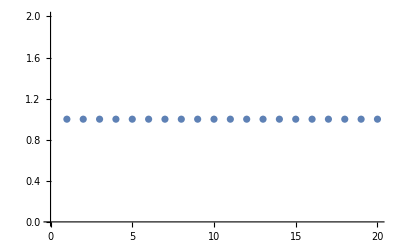

```mathematica
ListPlot[{a11/A11}]
```

```mathematica
a12=Array[a2,3];
A12=Array[A2,3];
kk2=RandomVariate[CircularUnitaryMatrixDistribution[4]];
```

```mathematica
For[i=1,i<3,i++,
kk2=RandomVariate[CircularUnitaryMatrixDistribution[4]];
a12[[i]]=Re[(1/4^6)* Sum[Tr[PauliString2[i1,j1].PauliString2[i3,j3].PauliString2[i4,j4].ConjugateTranspose[kk2].PauliString2[i,j].kk2]*Tr[PauliString2[i1,j1].PauliString2[i4,j4].ConjugateTranspose[kk2].PauliString2[i,j].kk2.PauliString2[i4,j4]]*Tr[PauliString2[i3,j3].ConjugateTranspose[kk2].PauliString2[i,j].kk2]*Tr[PauliString2[i4,j4].ConjugateTranspose[kk2].PauliString2[i,j].kk2],{i,0,3},{i1,0,3},{i2,0,3},{i3,0,3},{i4,0,3},{j,0,3},{j1,0,3},{j2,0,3},{j3,0,3},{j4,0,3}]];
A12[[i]]=Re[Tr[Q2.KroneckerProduct[kk2†,kk2†,kk2†,kk2†].Q2.KroneckerProduct[kk2,kk2,kk2,kk2].permutationMatrix[Flatten[permdouble[[9]]]]]];
]
a12
A12
```

{-5.33487,-4.64323,a2[3]}

{-0.33343,-0.290202,A2[3]}

```mathematica
a12/A12
```

{16.,16.,a2[3]/A2[3]}

0.991385

```mathematica
15.862160074458327/0.9913850046536458
```

16.

```mathematica
a12=4^6*a12;
A12=4^6*A12;
```

```mathematica
a12/A12
```

{16.,16.,16.}

```mathematica
kk2=RandomVariate[CircularUnitaryMatrixDistribution[4]];
```

```mathematica
a12[[3]]=Sum[Tr[PauliString2[i1,j1].PauliString2[i3,j3].PauliString2[i4,j4].ConjugateTranspose[kk2].PauliString2[i,j].kk2]*Tr[PauliString2[i1,j1].PauliString2[i4,j4].ConjugateTranspose[kk2].PauliString2[i,j].kk2.PauliString2[i4,j4]]*Tr[PauliString2[i3,j3].ConjugateTranspose[kk2].PauliString2[i,j].kk2]*Tr[PauliString2[i4,j4].ConjugateTranspose[kk2].PauliString2[i,j].kk2],{i,0,3},{i1,0,3},{i2,0,3},{i3,0,3},{i4,0,3},{j,0,3},{j1,0,3},{j2,0,3},{j3,0,3},{j4,0,3}];
```

```mathematica
A12[[3]]=4^6*Re[Tr[Q2.KroneckerProduct[kk2†,kk2†,kk2†,kk2†].Q2.KroneckerProduct[kk2,kk2,kk2,kk2].permutationMatrix[Flatten[permdouble[[9]]]]]]
```

95.7107

```mathematica
aa12=4^2*Re[Sum[Tr[PauliString2[i4,j4].kk2†.PauliString2[i,j].kk2.PauliString2[i4,j4].kk2†.PauliString2[i,j].kk2.PauliString2[i4,j4].kk2†.PauliString2[i,j].kk2]*Tr[PauliString2[i4,j4].kk2†.PauliString2[i,j].kk2],{i,0,3},{j,0,3},{i4,0,3},{j4,0,3}]]
```

95.7107

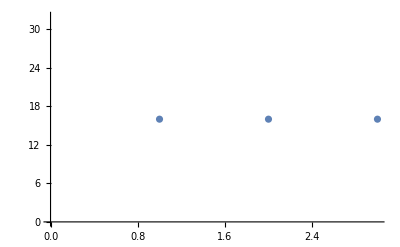

```mathematica
ListPlot[a12/A12]
```

```mathematica
Re[Tr[Q2.KroneckerProduct[kk2†,kk2†,kk2†,kk2†].Q2.KroneckerProduct[kk2,kk2,kk2,kk2].permutationMatrix[Flatten[{{5,6},{1,2},{3,4},{7,8}}]]]]/Re[Tr[Q2.KroneckerProduct[kk2†,kk2†,kk2†,kk2†].Q2.KroneckerProduct[kk2,kk2,kk2,kk2].permutationMatrix[Flatten[{{7,8},{3,4},{1,2},{5,6}}]]]]
```

1.

```mathematica
Permute[{{1,2},{3,4},{5,6},{7,8}},Cycles[{{1,3,4}}]]
```

{{7,8},{3,4},{1,2},{5,6}}

```mathematica
Dimensions[PauliString2[2,1]]
```

{4,4}

```mathematica
a24=(1/24)*(1/2^6)*2*Sum[Tr[PauliString1[i1].kk1†.PauliString1[i].kk1]*Tr[PauliString1[i1].kk1†.PauliString1[i].kk1]*Tr[PauliString1[i2].PauliString1[i1].kk1†.PauliString1[i].kk1]*Tr[PauliString1[i1].PauliString1[i2].kk1†.PauliString1[i].kk1],{i,0,3},{i1,0,3},{i2,0,3}]
```

0.0833333+0. ⅈ

```mathematica
2^7
```

128

```mathematica
a2try=(1/2^6)*Sum[Tr[PauliString1[i1].kk1†.PauliString1[i].kk1]*Tr[PauliString1[i2].kk1†.PauliString1[i].kk1]*Tr[PauliString1[i3].kk1†.PauliString1[i].kk1]*Tr[PauliString1[i4].kk1†.PauliString1[i].kk1]*Tr[KroneckerProduct[PauliString1[i1],PauliString1[i2],PauliString1[i3],PauliString1[i4]].P1],{i,0,3},{i1,0,3},{i2,0,3},{i3,0,3},{i4,0,3}]
```

2.+0. ⅈ

```mathematica
a2act=Tr[KroneckerProduct[kk1†,kk1†,kk1†,kk1†].Q1.KroneckerProduct[kk1,kk1,kk1,kk1].P1]
```

2.-1.70581×10^-17 ⅈ

```mathematica
a1try=(1/2^6)*Sum[Tr[PauliString1[i1].kk1†.PauliString1[i].kk1]*Tr[PauliString1[i2].kk1†.PauliString1[i].kk1]*Tr[PauliString1[i3].kk1†.PauliString1[i].kk1]*Tr[PauliString1[i4].kk1†.PauliString1[i].kk1]*Tr[KroneckerProduct[PauliString1[i1],PauliString1[i2],PauliString1[i3],PauliString1[i4]].Q1.P1],{i,0,3},{i1,0,3},{i2,0,3},{i3,0,3},{i4,0,3}]
```

0.444208+0. ⅈ

```mathematica
a1act=a2act=Tr[KroneckerProduct[kk1†,kk1†,kk1†,kk1†].Q1.KroneckerProduct[kk1,kk1,kk1,kk1].Q1.P1]
```

0.444208+6.93889×10^-18 ⅈ

```mathematica
(1/4)*Sum[Tr[PauliString1[2].PauliString1[i]]*Tr[PauliString1[2].PauliString1[i]]*Tr[PauliString1[2].PauliString1[i]]*Tr[PauliString1[2].PauliString1[i]],{i,0,3}]
```

4

```mathematica
twofour=(1/4)Sum[Tr[KroneckerProduct[PauliString1[1].PauliString1[i],PauliString1[0].PauliString1[i],PauliString1[1].PauliString1[i],PauliString1[0].PauliString1[i]].permutationMatrix[{1,4,3,2}]],{i,0,3}]
```

2

```mathematica
k1=RandomVariate[CircularUnitaryMatrixDistribution[2]];
k2=RandomVariate[CircularUnitaryMatrixDistribution[2]];
k3=RandomVariate[CircularUnitaryMatrixDistribution[2]];
k4=RandomVariate[CircularUnitaryMatrixDistribution[2]];
```

```mathematica
Tr[KroneckerProduct[k1,k2,k3,k4].permutationMatrix[Flatten[permsingle[[9]]]]]
Tr[k4]*Tr[k2.k3.k1]
```

-0.250755-0.21477 ⅈ

-0.250755-0.21477 ⅈ

```mathematica
Permute[{1,2,3,4},Cycles[{{1,3,2}}]]
```

{2,3,1,4}

```mathematica
permsingle
```

{{1,2,3,4},{1,2,4,3},{1,3,2,4},{1,3,4,2},{1,4,2,3},{1,4,3,2},{2,1,3,4},{2,1,4,3},{2,3,1,4},{2,3,4,1},{2,4,1,3},{2,4,3,1},{3,1,2,4},{3,1,4,2},{3,2,1,4},{3,2,4,1},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,1,3,2},{4,2,1,3},{4,2,3,1},{4,3,1,2},{4,3,2,1}}

```mathematica
onethreetwo=(1/4)*Sum[Tr[KroneckerProduct[PauliString1[0].PauliString1[i],PauliString1[0].PauliString1[i],PauliString1[0].PauliString1[i],PauliString1[0].PauliString1[i]].permutationMatrix[Flatten[permsingle[[9]]]]],{i,0,3}]
```

```mathematica
kk1=RandomVariate[CircularUnitaryMatrixDistribution[2]];
F1=Tr[KroneckerProduct[kk1†,kk1†,kk1†,kk1†].Q1.KroneckerProduct[kk1,kk1,kk1,kk1].Q1.P1]
ff1=(1/(6*2^6))*(3*2^7+2^6*Tr[Q1.KroneckerProduct[kk1†,kk1†,kk1†,kk1†].Q1.KroneckerProduct[kk1,kk1,kk1,kk1]]+(2*2^2)*Sum[Tr[(PauliString1[i4].kk1†.PauliString1[i].kk1).(PauliString1[i4].kk1†.PauliString1[i].kk1).(PauliString1[i4].kk1†.PauliString1[i].kk1)]*Tr[(PauliString1[i4].kk1†.PauliString1[i].kk1)],{i,0,3},{i4,0,3}])
ff1/F1
```

0.731624+1.56125×10^-17 ⅈ

1.36581+9.54098×10^-18 ⅈ

1.86682-2.67962×10^-17 ⅈ

```mathematica
Permute[{1,2,3,4},Cycles[{{1,2,3}}]]
```

{3,1,2,4}

```mathematica
Sum[Tr[(PauliString1[i4].kk1†.PauliString1[i].kk1).(PauliString1[i4].kk1†.PauliString1[i].kk1).(PauliString1[i4].kk1†.PauliString1[i].kk1)]*Tr[(PauliString1[i4].kk1†.PauliString1[i].kk1)],{i,0,3},{i4,0,3}]
```

-11.0764+0. ⅈ

```mathematica
2^4*Re[Tr[Q1.KroneckerProduct[kk1†,kk1†,kk1†,kk1†].Q1.KroneckerProduct[kk1,kk1,kk1,kk1].permutationMatrix[{3,1,2,4}]]]
```

-11.0764

```mathematica
kk1=RandomVariate[CircularUnitaryMatrixDistribution[2]];
aid=4*Re[Sum[Tr[PauliString1[i4].kk1†.PauliString1[i].kk1]^4,{i,0,3},{i4,0,3}]];
a12=2*Re[Sum[Tr[PauliString1[i4].kk1†.PauliString1[i].kk1]*Tr[PauliString1[i4].kk1†.PauliString1[i].kk1]*Tr[PauliString1[i1].PauliString1[i4].kk1†.PauliString1[i].kk1]*Tr[PauliString1[i4].PauliString1[i1].kk1†.PauliString1[i].kk1],{i1,0,3},{i4,0,3},{i,0,3}]];
a14=2*Re[Sum[Tr[PauliString1[i2].kk1†.PauliString1[i].kk1]*Tr[PauliString1[i2].kk1†.PauliString1[i].kk1]*Tr[PauliString1[i1].PauliString1[i2].kk1†.PauliString1[i].kk1]*Tr[PauliString1[i2].PauliString1[i1].kk1†.PauliString1[i].kk1],{i,0,3},{i1,0,3},{i2,0,3}]];
a24=a14;

a132=Re[Sum[Tr[PauliString1[i1].PauliString1[i4].kk1†.PauliString1[i].kk1.PauliString1[i4]]*Tr[PauliString1[i1].PauliString1[i3].PauliString1[i4].kk1†.PauliString1[i].kk1]*Tr[PauliString1[i4].kk1†.PauliString1[i].kk1]*Tr[PauliString1[i3].kk1†.PauliString1[i].kk1],{i,0,3},{i1,0,3},{i3,0,3},{i4,0,3}]];
a123=a132;
F1=Re[Tr[KroneckerProduct[kk1†,kk1†,kk1†,kk1†].Q1.KroneckerProduct[kk1,kk1,kk1,kk1].Q1.P1]]
fff1=(1/(6*2^6))*(aid+a12+a24+a14+a132+a123)
```

0.327292

1.16365

1.22573

```mathematica
F1
```

0.307723-2.77556×10^-17 ⅈ

```mathematica
Permute[{1,2,3,4},Cycles[{{1,3,2}}]]
```

{2,3,1,4}

```mathematica
PermutationCycles[{4,3,1,2}]
```

Cycles[{{1,4,2,3}}]

```mathematica
kk14=KroneckerProduct[kk1,kk1,kk1,kk1];
```

```mathematica
newnewnewexpress1=Re[(1/(6*2^6))*((2^6)*Tr[Q1.kk14†.Q1.kk14]+3*(2^6)*Tr[(Q1.kk14†.Q1.kk14).permutationMatrix[{1,2,4,3}]]+2*(2^6)*Tr[(Q1.kk14†.Q1.kk14).permutationMatrix[Flatten[permsingle[[9]]]]])]
```

0.327292

```mathematica
a1=Re[Tr[kk14†.Q1.kk14.Q1.P1]]
```

0.327292

```mathematica
a11one=Array[a1,20];
A11one=Array[A1,20];
```

a1[1]

```mathematica
For[i=1,i<21,i++,
kk1=RandomVariate[CircularUnitaryMatrixDistribution[2]];
kk14=KroneckerProduct[kk1,kk1,kk1,kk1];
a11one[[i]]=Re[(1/(6*2^6))*((2^6)*Tr[Q1.kk14†.Q1.kk14]+3*(2^6)*Tr[(Q1.kk14†.Q1.kk14).permutationMatrix[Flatten[permsingle[[2]]]]]+2*(2^6)*Tr[(Q1.kk14†.Q1.kk14).permutationMatrix[Flatten[permsingle[[9]]]]])];
A11one[[i]]=Re[Tr[kk14†.Q1.kk14.Q1.P1]];
]
```

```mathematica
a11one/A11one
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
a11two=Array[a2,100];
A11two=Array[A2,100];
```

```mathematica
Do[
kk2=RandomVariate[CircularUnitaryMatrixDistribution[4]];
kk24=KroneckerProduct[kk2,kk2,kk2,kk2];
a11two[[i]]=Re[(1/(6*4^6))*((4^6)*Tr[Q2.kk24†.Q2.kk24]+3*(4^6)*Tr[(Q2.kk24†.Q2.kk24).permutationMatrix[Flatten[permdouble[[2]]]]]+2*(4^6)*Tr[(Q2.kk24†.Q2.kk24).permutationMatrix[Flatten[permdouble[[9]]]]])];
A11two[[i]]=Re[Tr[kk24†.Q2.kk24.Q2.P2]];
,{i,1,100}]
```

```mathematica
a11two/A11two
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

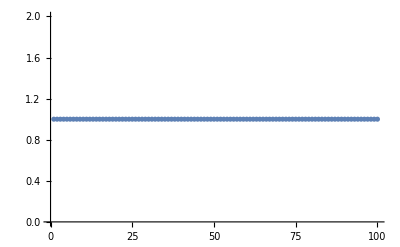

```mathematica
ListPlot[a11two/A11two]
```

## TUPLE STUFF

```mathematica
n=3;
d=2^n;
x=Tuples[{0,1},n];
xp=Tuples[{0,1},n];
zp=Tuples[{0,1},n];
k=Tuples[{0,1},n];
kp=Tuples[{0,1},n];
z=Tuples[{0,1},n];
j=Tuples[{0,1},n];
jp=Tuples[{0,1},n];

o=Exp[2*π*I/Length[x]];
oc=Conjugate[o];
```

{0,0,0}

```mathematica
Dimensions[trupup]
```

{4,4,4,4}

```mathematica
truquq=Simplify[1/Length[x]^8*Sum[trupup[[i,k,l,m]]^4,{i,1,Length[x]},{k,1,Length[x]},{l,1,Length[x]},{m,1,Length[x]}]]
```

79507/4096

```mathematica
UFT14=KroneckerProduct[UFT1,UFT1,UFT1,UFT1];
UFT24=KroneckerProduct[UFT2,UFT2,UFT2,UFT2];


1/Length[x]^4 Sum[Tr[PauliString2[i1,j1].UFT2†.PauliString2[i2,j2].UFT2]^4,{i1,0,3},{j1,0,3},{i2,0,3},{j2,0,3}]
```

7

```mathematica
Tr[UFT24†.Q2.UFT24.Q2]
```

7

```mathematica
Tr[Q1.UFT14†.Q1.UFT14]
```

4

```mathematica
UFT3=FourierMatrix[8];
UFT34=KroneckerProduct[UFT3,UFT3,UFT3,UFT3];
```

```mathematica
Tr[UFT34†.Q3.UFT34.Q3]
```

$Aborted

```mathematica
Simplify[1/8^4 Parallelize[Sum[Tr[PauliString3[i1,j1,k1].UFT3†.PauliString3[i2,j2,k2].UFT3]^4,{i1,0,3},{j1,0,3},{k1,0,3},{i2,0,3},{j2,0,3},{k2,0,3}]]]
```

29/2

```mathematica
PauliString5[i_,j_,k_,l_,m_]=KroneckerProduct[PauliString1[i],PauliString1[j],PauliString1[k],PauliString1[l],PauliString1[m]];
```

```mathematica
UFT4=FourierMatrix[16];
```

```mathematica
Simplify[1/16^4 Parallelize[Sum[Tr[PauliString4[i1,j1,k1,l1].UFT4†.PauliString4[i2,j2,k2,l2].UFT4]^4,{i1,0,3},{j1,0,3},{k1,0,3},{l1,0,3},{i2,0,3},{j2,0,3},{k2,0,3},{l2,0,3}]]]
```

1/32 (920+117 √2)

```mathematica
UFT5=FourierMatrix[2^5];
Simplify[1/32^4 Parallelize[Sum[Tr[PauliString5[i1,j1,k1,l1,m1].UFT5†.PauliString5[i2,j2,k2,l2,m2].UFT5]^4,{i1,0,3},{j1,0,3},{k1,0,3},{l1,0,3},{m1,0,3},{i2,0,3},{j2,0,3},{k2,0,3},{l2,0,3},{m2,0,3}]]]
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of the TimeConstraint option may improve the result of simplification.

$Aborted

```mathematica
t=Table[Sum[KroneckerDelta[j[[i1]],Mod[jp[[j1]]+x[[i]],2]]*KroneckerDelta[j[[i2]],Mod[jp[[j2]]+x[[i]],2]]*KroneckerDelta[j[[i3]],Mod[jp[[j3]]+x[[i]],2]]*KroneckerDelta[j[[i4]],Mod[jp[[j4]]+x[[i]],2]],{i,1,Length[x]}],{i1,1,Length[x]},{j1,1,Length[x]},{i2,1,Length[x]},{j2,1,Length[x]},{i3,1,Length[x]},{j3,1,Length[x]},{i4,1,Length[x]},{j4,1,Length[x]}];
```

```mathematica
tt=Flatten[t];
```

```mathematica
Tally[tt]
```

{{1,1024},{0,64512}}

```mathematica
ttt=Table[t[[i,Mod[i+1,4]+1,k,Mod[k+1,4]+1,l,Mod[l+1,4]+1,m,Mod[m+1,4]+1]],{i,1,Length[x]},{k,1,Length[x]},{l,1,Length[x]},{m,1,Length[x]}];
Tally[Flatten[ttt]]
```

{{1,256}}

```mathematica
tp=Table[Sum[KroneckerDelta[x[[i]],Mod[jp[[j1]]+j[[i1]],2]]*KroneckerDelta[x[[i]],Mod[jp[[j2]]+j[[i2]],2]]*KroneckerDelta[x[[i]],Mod[jp[[j3]]+j[[i3]],2]]*KroneckerDelta[x[[i]],Mod[jp[[j4]]+j[[i4]],2]],{i,1,Length[x]}],{i1,1,Length[x]},{j1,1,Length[x]},{i2,1,Length[x]},{j2,1,Length[x]},{i3,1,Length[x]},{j3,1,Length[x]},{i4,1,Length[x]},{j4,1,Length[x]}];
```

```mathematica
stringtoint[m_]:=Sum[2^(Length[m]-i-1)*m[[i+1]],{i,0,Length[m]-1}]
```

```mathematica
uft2=1/(√d)Table[o^(stringtoint[j[[i]]]*stringtoint[j[[k]]]),{i,1,d},{k,1,d}];
```

```mathematica
UFT2//MatrixForm
```

(1/2 | 1/2 | 1/2 | 1/2
1/2 | ⅈ/2 | -1/2 | -ⅈ/2
1/2 | -1/2 | 1/2 | -1/2
1/2 | -ⅈ/2 | -1/2 | ⅈ/2)

```mathematica
uu2=1/(√d)Table[o^(j[[i]].j[[l]]),{i,1,d},{l,1,d}];
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}